```mathematica
w[x_,nodes_]:=(
expr=1;
For[i=1,i≤Length[nodes],i++,expr*=x-nodes[[i]]];
expr//Simplify
)
```

```mathematica
w[x,{1,2,3,4}]
```

(-4+x) (-3+x) (-2+x) (-1+x)

```mathematica
wk[x,nodes_,k_] := w[x,nodes]/(x-nodes[[k]])
```

```mathematica
wk[x,{1, 2, 3, 4}, 2]
```

(-4+x) (-3+x) (-1+x)

```mathematica
lk[x_, nodes_, k_]:=wk[x,nodes,k]/(wk[x, nodes,k]/.{x-> nodes[[k]]})
```

```mathematica
lk[x, {1, 2, 4, 6}, 1]
```

-1/15 (-6+x) (-4+x) (-2+x)

```mathematica
Lagrange[nodes_,values_,x_]:=(
poly=0;
For[j=1,j≤Length[nodes],j++,poly+=values[[j]] * lk[x,nodes,j];];
poly //Simplify
)
```

```mathematica
p[x_]=Lagrange[{1,2,4,6},{2,9,41,97},x]
```

1-2 x+3 x^2

```mathematica
f[x_]=Lagrange[Range[0, 120000,30000], {9.81,9.7487,9.6879,9.6278,9.5682}, x]
f[55000]
```

9.81-2.04611×10^-6 x-3.7037×10^-14 x^2+4.93827×10^-18 x^3-2.05761×10^-23 x^4

9.69799

Задача3:

```mathematica
z3nodes :={0, Pi/4, Pi/2}
z3values=Map[Cos,z3nodes]
```

{1,1/(√2),0}

```mathematica
Lpoly[x_]=Lagrange[z3nodes, z3values, x]//Expand
```

1-(6 x)/π+(4 √2 x)/π+(8 x^2)/π^2-(8 √2 x^2)/π^2

```mathematica
Lerr[x_]:=Abs[(Cos[x]-Lpoly[x])/Cos[x]]
Hpoly[x_]:=1-(4x^2)/(Pi^2)
```

```mathematica
Herr[x_]:=Abs[(Cos[x]-Hpoly[x])/Cos[x]]
```

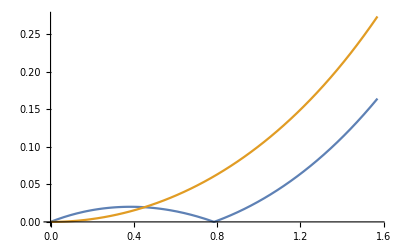

```mathematica
Plot[{Lerr[x],Herr[x]},{x, 0, Pi/2}]
```

```mathematica
sinErr1[x_]=Abs[(N[Sin[1]]/24)*w[x,{-1, -0.3, 0.3, 1}]]
```

0.0350613 Abs[(-1+x) (-0.3+x) (0.3+x) (1+x)]

```mathematica
Tnodes[k_]:=Cos[((2*k-1)*Pi)/6]//N
```

```mathematica
sinErr2[x_]=Abs[(N[Sin[1]]/24)*w[x, Map[Tnodes, {1, 2, 3, 4}]]]
```

0.0350613 Abs[(-0.866025+x) (0.+x) (0.866025+x)^2]

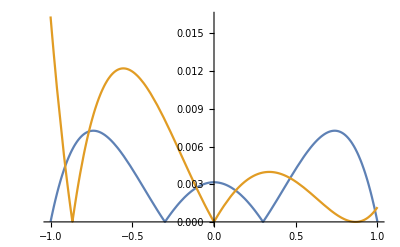

```mathematica
Plot[{sinErr1[x], sinErr2[x]},{x, -1, 1}]
```